## Testing the effectiveness of ZPS in mitigating errors for one - loss cat code

M . Bergmann and P . van Loock, PRA 94, 042332 (2016)

```mathematica
𝒜:=1/(2 Cosh[T α^2]);

p0 := 𝒜 Cosh[γ T α^2](Cosh[(1-γ)T α^2]+Cos[(1-γ)T α^2]) ;
p1 := 𝒜 Sinh[γ T α^2](Sinh[(1-γ)T α^2]+Sin[(1-γ)T α^2]) ;
p2 := 𝒜 Cosh[γ T α^2](Cosh[(1-γ)T α^2]-Cos[(1-γ)T α^2]) ;
p3 := 𝒜 Sinh[γ T α^2](Sinh[(1-γ)T α^2]-Sin[(1-γ)T α^2]) ;

𝒩:=1/(1+2Re[a b*] Cos[T α^2]/Cosh[T α^2]);

p0Tilde[a_,b_,α_,T_,γ_] = 𝒩  p0 (1+2 Re[a b*] Cos[γ T α^2]/Cosh[γ T α^2]);
p1Tilde[a_,b_,α_,T_,γ_] = 𝒩  p1 (1-2 Re[a b*] Sin[γ T α^2]/Sinh[γ T α^2]);
p2Tilde[a_,b_,α_,T_,γ_] = 𝒩  p2 (1-2 Re[a b*] Cos[γ T α^2]/Cosh[γ T α^2]);
p3Tilde[a_,b_,α_,T_,γ_] = 𝒩  p3 (1+2 Re[a b*] Sin[γ T α^2]/Sinh[γ T α^2]);
```

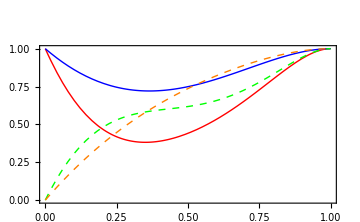

```mathematica
(* probability of correctable errors - including no error - this is just 1-PU*)
PC[a_,b_,α_,T_,γ_]=p0Tilde[a,b,α,T,γ]+p1Tilde[a,b,α,T,γ];

Module[{a,b,α,T1,T2,γ,plt,txt,text,xlab,ylab},
a=1/(√2);
b =a;
α = 2;
T1=1;
T2=.5;

titleSize = 20;
axesLabelSize = 20;
fam = "CMU Sans Serif";

text=Text[Style["a",{FontSize->titleSize,FontFamily->fam,Black,Bold}],{.5,1.2},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,0},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["P_C"
,{FontSize->axesLabelSize,FontFamily->fam,Black}],{.0,1.12},{0,0}];
ylab = Graphics[{ylabel}];

plt = Plot[{PC[a,b,α,T1,γ],PC[a,b,α,T2,γ],PC[a,-b,α,T1,γ],PC[a,-b,α,T2,γ]},{γ, 0,1},PlotRange->{0,1},LabelStyle->{FontSize->20,FontFamily->"CMU Sans Serif",Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Red,Thick},{Blue,Thick},{Green, Dashed,Thick},{Orange, Dashed,Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None];

Show[{plt, txt,xlab,ylab}]
]
```

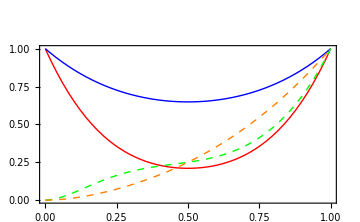

```mathematica
(* probability of mitigation *)
PM[a_,b_,α_,T_,γ_]=p0Tilde[a,b,α,T,γ];

Module[{a,b,α,T1,T2,γ,plt,txt,text,xlab,ylab},
a=1/(√2);
b =a;
α = 2;
T1=1;
T2=.5;

titleSize = 20;
axesLabelSize = 20;
fam = "CMU Sans Serif";

text=Text[Style["b",{FontSize->titleSize,FontFamily->fam,Black,Bold}],{.5,1.2},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,0},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["P_M",{FontSize->axesLabelSize,FontFamily->fam,Black}],{.0,1.12},{0,0}];
ylab = Graphics[{ylabel}];


plt = Plot[{PM[a,b,α,T1,γ],PM[a,b,α,T2,γ],PM[a,-b,α,T1,γ],PM[a,-b,α,T2,γ]},{γ, 0,1},PlotRange->{0,1},LabelStyle->{FontSize->20,FontFamily->"CMU Sans Serif",Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Red,Thick},{Blue,Thick},{Green, Dashed,Thick},{Orange, Dashed,Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None];

Show[{plt, txt,xlab,ylab}]
]
```

```mathematica
titleSize = 20;
axesLabelSize = 20;

text=Text[Style["c",{FontSize->titleSize,FontFamily->"CMU Sans Serif",Black,Bold}],{.5,.5},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->"CMU Sans Serif",Black}],{1.08,-1},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["(p̃)_1-P_U",{FontSize->axesLabelSize,FontFamily->"CMU Sans Serif",Black}],{.05,0.48},{0,0}];
ylab = Graphics[{ylabel}];
```

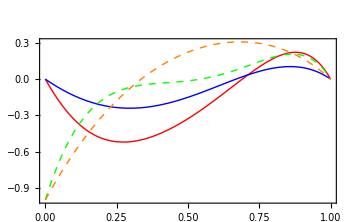

```mathematica
(* difference in probabilities of truly correctable errors v. uncorrectable errors *)
diff[a_,b_,α_,T_,γ_]=p1Tilde[a,b,α,T,γ]-PU[a,b,α,T,γ] ;

Module[{a,b,α,T1,T2,γ,plt,txt,text,xlab,ylab},
a=1/(√2);
b =a;
α = 2;
T1=1;
T2=.5;

titleSize = 20;
axesLabelSize = 20;

titleSize = 20;
axesLabelSize = 20;
fam = "CMU Sans Serif";

text=Text[Style["c",{FontSize->titleSize,FontFamily->fam,Black,Bold}],{.5,0.52},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{1.08,0},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["(p̃)_1-P_U",{FontSize->axesLabelSize,FontFamily->fam,Black}],{.05,0.48},{0,0}];
ylab = Graphics[{ylabel}];


plt = Plot[{diff[a,b,α,T1,γ],diff[a,b,α,T2,γ],diff[a,-b,α,T1,γ],diff[a,-b,α,T2,γ]},{γ, 0,1},PlotRange->Full,LabelStyle->{FontSize->20,FontFamily->"CMU Sans Serif",Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Red,Thick},{Blue,Thick},{Green, Dashed,Thick},{Orange, Dashed,Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None];

Show[{plt, txt,xlab,ylab}]
]
```

## Noisy ZPS vs noise after ideal ZPS

Input is an even two-component cat, of the form μ̄= 𝒩_+(ⅈ^μ α+-ⅈ^μα)

```mathematica
(* noisy ZPS *)

pLnoisyZPS[α_,T_,η_]=(Cosh[T α^2]Cosh[(1-η)(1-T)α^2])/Cosh[(1-η(1-T))α^2] ; (* probaility to stay logical *)
pEnoisyZPS[α_,T_,η_]=1-pLnoisyZPS[α,T,η] ;(* probaility of an error *)

(* ZPS then loss *)

pLZPSloss[β_,T_,γ_]= pLnoisyZPS[√T β,γ,0] ; (* probability to stay logical *)
pEZPSloss[β_,T_,γ_]=1-pLZPSloss[β,T,γ] ;(* probability of an error *)
```

```mathematica
Simplify[Solve[FullSimplify[pLnoisyZPS[α ,T,η]-pLZPSloss[√(1/γ)α ,T,γ]]==0,γ][[1]],{0<γ<1,0<T<1,α>0,0<η<1}]
```

{γ→ConditionalExpression[(T α^2)/(-ArcTanh[Coth[T α^2] (-1+Cosh[(-1+T) α^2 (-1+η)] Sech[T α^2] Sech[α^2 (1+(-1+T) η)])]+ⅈ π C[1]), C[1]∈ℤ]}

```mathematica
ℽ[α_,T_,η_]=(T α^2)/(-ArcTanh[Coth[T α^2] (-1+Cosh[(-1+T) α^2 (-1+η)] Sech[T α^2] Sech[α^2 (1+(-1+T) η)])]);
```

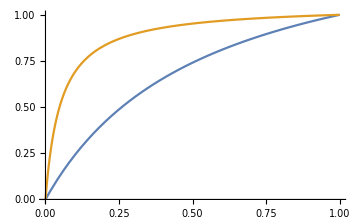

```mathematica
Plot[{ℽ[2,T,.65],ℽ[2,T,.95]},{T,0,1},FrameLabel->Automatic,LabelStyle->{FontSize->Large,FontFamily->"CMU Sans Serif",Black},ImageSize->Medium]
```

```mathematica
(* Plot *)
cols=Reverse[RGBColor/@{(*"#053061","#2166ac",*)"#4393c3","#92c5de","#d1e5f0","#f7f7f7","#fddbc7","#f4a582","#d6604d"(*,"#b2182b","#67001f"*)}];
Manipulate[
Module[{η},
η=0.65;
plt1 = Plot[ℽ[α,T,η],{T,0,1}];
plt2 = DensityPlot[HeavisideTheta[pLnoisyZPS[α ,T,η]-pLZPSloss[√(1/γ)α ,T,γ]],{T,0,1},{γ,0,1},ColorFunction->(Blend[cols,#]&),ColorFunctionScaling->True,FrameLabel->Automatic,LabelStyle->{FontSize->Large,FontFamily->"CMU Sans Serif",Black},ImageSize->Medium];

Show[{plt2,plt1}]
]
,{α,1,4}]
```

## Composition of lossy bosonic channels

Here we study the composition of two LBCs (γ1 and γ2) on an cats

From iPad notes - “Cat via noisy Threshold ZPS” we have

```mathematica
(* probability Subscript[P, xy] of x-parity cat output and y-parity cat input *)
Pee[α_,γ_]=(Cosh[(γ)α^2]Cosh[(1-γ)α^2])/Cosh[α^2];
Poe[α_,γ_]=(Sinh[(γ)α^2]Sinh[(1-γ)α^2])/Cosh[α^2];
Peo[α_,γ_]=(Cosh[(γ)α^2]Sinh[(1-γ)α^2])/Sinh[α^2];
Poo[α_,γ_]=(Sinh[(γ)α^2]Cosh[(1-γ)α^2])/Sinh[α^2];
```

```mathematica
p1 =Simplify[Pee[√γ1 α,γ2]Pee[α,γ1]+Peo[√γ1 α,γ2]Poe[α,γ1]]
p2 =Simplify[Poe[√γ1 α,γ2]Pee[α,γ1]+Poo[√γ1 α,γ2]Poe[α,γ1]]
```

Cosh[α^2 γ1 γ2] Cosh[α^2 (1-γ1 γ2)] Sech[α^2]

Sech[α^2] Sinh[α^2 γ1 γ2] Sinh[α^2 (1-γ1 γ2)]

This tells that the effective transmission is simply the product of the two transmissions